#### Trajectory equation

```mathematica
x[η_,η0_]:=α/(α-1)η(1-(η/η0)^α)
(*x[η_,η0_]:=α(η0-η+Log[η/η0])*)
```

#### Trajectory profile

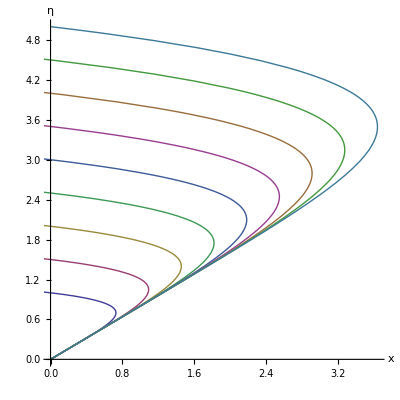

```mathematica
α=5;
η0m=5;
ParametricPlot[
Table[{x[η,η0],η},{η0,1,η0m,(η0m-1)/8}]//Evaluate,
{η,0,η0m},PlotRange->{{0,Automatic},All},
PlotStyle->Thick,
AxesLabel->{"x","η"},AxesStyle->Directive[FontSize->18],
GridLines->None]
(*,AspectRatio->2.2]*)
```

#### PDF

```mathematica
η0[η_,Δ_?NumericQ]:=η0/.FindRoot[x[η,η0]==Δ,{η0,1}]//Re//Quiet
v[η_,η0_]:=√((η-x[η,η0])^2+(η/α)^2)
p0[η0_]:=√(α/(2π))Exp[-α/2 η0^2]
(* ρ is 2D PDF; pθ is marginalised over Δ *)
ρ[η_,η0_?NumericQ]:=(α-1)/α(η0/η)^(α+1)Abs[1-(α+1)(η/η0)^α]/(√((1-(α+1)(η/η0)^α)^2+(α-1)^2))*v[η,η0]/v[η0,η0]*p0[η0]*HeavisideTheta[η-x[η,η0]]
```

```mathematica
ContourPlot[ρ[η,η0[η,δ]//Evaluate],
{δ,0,0.5},{η,0,1},
FrameLabel->{"x","η"},FrameStyle->Directive[FontSize->18],
PlotLegends->Automatic]
```

-Graphics-

#### Spatial PDF

```mathematica
Manipulate[Plot[ρ[η,η0[η,Δ]],{η,0,1.0}],{Δ,0,0.5}]
```

```mathematica
Q[Δ_]:=NIntegrate[ρ[η,η0[η,Δ]],{η,0,10α}]//Quiet
```

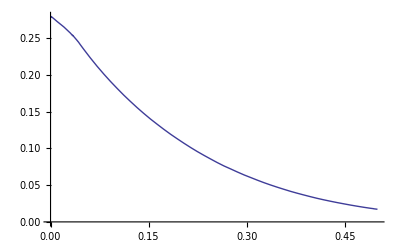

```mathematica
Plot[Q[δ],{δ,0,0.5}]
```

#### Pressure

```mathematica
Clear[α]
NIntegrate[δ*Q[δ]/.{α->5.0},{δ,0,2}]
```

NIntegrate::nlim: η = 10.\ α is not a valid limit of integration.

NIntegrate::inumr: The integrand ρ[η, η0[η, δ]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 50.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate[δ Q[δ]/.{α→5.},{δ,0,2}]